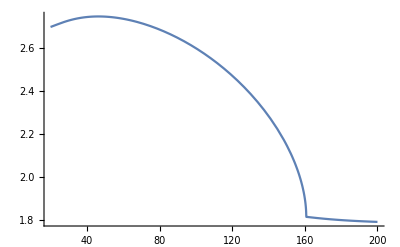

```mathematica
Me=.0000511;
Mμ=.1057;
Mτ=1.777;
MW=80.4;
Mu= 0.0023;
Md= 0.0048;
Ms = 0.095;
Mc = 1.4;
Mt = 172;
Mb  = 4.2;
Bem[Mx_]=-11/3;
taue[Mx_]=4*(Me^2)/(Mx^2);
tauμ[Mx_]=4*(Mμ^2)/(Mx^2);
tauτ[Mx_]=4*(Mτ^2)/(Mx^2);
tauW[Mx_]=4*(MW^2)/(Mx^2);
tauu[Mx_]=4*(Mu^2/(Mx)^2);
taud[Mx_]=4*(Md^2/(Mx)^2);
taus[Mx_]=4*(Ms^2/(Mx)^2);
tauc[Mx_]=4*(Mc^2/(Mx)^2);
taut[Mx_]=4*(Mt^2/(Mx)^2);
taub[Mx_] = 4*(Mb^2/(Mx)^2);
ft[taui_]=Piecewise[{{(ArcSin[Sqrt[1/taui]])^2,taui≥1},{(-1/4)*(Log[(1+Sqrt[1-taui])/(1-Sqrt[1-taui])]-ⅈ*π)^2,taui<1}}];
F1[tau1_]=2+3*tau1+(3*tau1)*(2-tau1)*ft[tau1];
F12[tau12_]= -2*tau12*(1+(1-tau12)*ft[tau12]);
SumLoopCorrection[Mx_]=       F12[taue[Mx]]+F12[tauμ[Mx]]+F12[tauτ[Mx]]+F1[tauW[Mx]] + 3*(2/3)^2*F12[tauu[Mx]]+3*(-1/3)^2*F12[taud[Mx]]+ 3*(2/3)^2*F12[tauc[Mx]]+3*(-1/3)^2*F12[taus[Mx]]+ 3*(2/3)^2*F12[taut[Mx]]+3*(-1/3)^2*F12[taub[Mx]];
Rγ[Mx_]=(Abs[-Bem[Mx]+SumLoopCorrection[Mx]])^2/(Abs[SumLoopCorrection[Mx]])^2;
Plot[Rγ[Mx],{Mx,20,200}]
```